## Plotting L=12 all1 Spread Complexity

```mathematica
tList1 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_all1_state/L12/t_list_Delta_1_L_12_w_0_R_10_pbc.txt","Table"]//Flatten;
KCW0 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_all1_state/L12/complexity_Delta_1_L_12_w_0_R_10_pbc.txt","Table"]//Flatten;
KIPRW0 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_all1_state/L12/krylov_IPR_Delta_1_L_12_w_0_R_10_pbc.txt","Table"]//Flatten;
KEntW0 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_all1_state/L12/krylov_entropy_Delta_1_L_12_w_0_R_10_pbc.txt","Table"]//Flatten;
EntComplexityW0 = Exp[#] &/@ KEntW0;
```

```mathematica
KCpltW0=ListLinePlot[Transpose[{tList1,KCW0}],PlotRange->All];
```

```mathematica
tList2 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_all1_state/L12/t_list_Delta_1_L_12_w_0.01_R_10_pbc.txt","Table"]//Flatten;
KCW0pt01 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_all1_state/L12/complexity_Delta_1_L_12_w_0.01_R_10_pbc.txt","Table"]//Flatten;
KIPRW0pt01 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_all1_state/L12/krylov_IPR_Delta_1_L_12_w_0.01_R_10_pbc.txt","Table"]//Flatten;
KEntW0pt01 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_all1_state/L12/krylov_entropy_Delta_1_L_12_w_0.01_R_10_pbc.txt","Table"]//Flatten;
EntComplexityW0pt01 = Exp[#] &/@ KEntW0pt01;
```

```mathematica
KCpltW0pt01=ListLinePlot[Transpose[{tList1,KCW0pt01}],PlotRange->All];
```

```mathematica
tList3 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_all1_state/L12/t_list_Delta_1_L_12_w_0.1_R_10_pbc.txt","Table"]//Flatten;
KCW0pt1 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_all1_state/L12/complexity_Delta_1_L_12_w_0.1_R_10_pbc.txt","Table"]//Flatten;
KIPRW0pt1 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_all1_state/L12/krylov_IPR_Delta_1_L_12_w_0.1_R_10_pbc.txt","Table"]//Flatten;
KEntW0pt1 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_all1_state/L12/krylov_entropy_Delta_1_L_12_w_0.1_R_10_pbc.txt","Table"]//Flatten;
EntComplexityW0pt1 = Exp[#] &/@ KEntW0pt1;
```

```mathematica
KCpltW0pt1=ListLinePlot[Transpose[{tList3,KCW0pt1}],PlotRange->All];
```

```mathematica
tList4 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_all1_state/L12/t_list_Delta_1_L_12_w_0.2_R_10_pbc.txt","Table"]//Flatten;
KCW0pt2 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_all1_state/L12/complexity_Delta_1_L_12_w_0.2_R_10_pbc.txt","Table"]//Flatten;
KIPRW0pt2= Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_all1_state/L12/krylov_IPR_Delta_1_L_12_w_0.2_R_10_pbc.txt","Table"]//Flatten;
KEntW0pt2 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_all1_state/L12/krylov_entropy_Delta_1_L_12_w_0.2_R_10_pbc.txt","Table"]//Flatten;
EntComplexityW0pt2 = Exp[#] &/@ KEntW0pt2;
```

```mathematica
KCpltW0pt2=ListLinePlot[Transpose[{tList4,KCW0pt2}],PlotRange->All];
```

```mathematica
tList5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_all1_state/L12/t_list_Delta_1_L_12_w_0.5_R_10_pbc.txt","Table"]//Flatten;
KCW0pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_all1_state/L12/complexity_Delta_1_L_12_w_0.5_R_10_pbc.txt","Table"]//Flatten;
KIPRW0pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_all1_state/L12/krylov_IPR_Delta_1_L_12_w_0.5_R_10_pbc.txt","Table"]//Flatten;
KEntW0pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_all1_state/L12/krylov_entropy_Delta_1_L_12_w_0.5_R_10_pbc.txt","Table"]//Flatten;
EntComplexityW0pt5 = Exp[#] &/@ KEntW0pt5;
```

```mathematica
KCpltW0pt5=ListLinePlot[Transpose[{tList4,KCW0pt5}],PlotRange->All];
```

```mathematica
tList6 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_all1_state/L12/t_list_Delta_1_L_12_w_1_R_10_pbc.txt","Table"]//Flatten;
KCW1 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_all1_state/L12/complexity_Delta_1_L_12_w_1_R_10_pbc.txt","Table"]//Flatten;
KIPRW1 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_all1_state/L12/krylov_IPR_Delta_1_L_12_w_1_R_10_pbc.txt","Table"]//Flatten;
KEntW1 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_all1_state/L12/krylov_entropy_Delta_1_L_12_w_1_R_10_pbc.txt","Table"]//Flatten;
EntComplexityW1 = Exp[#] &/@ KEntW1;
```

```mathematica
KCpltW1=ListLinePlot[Transpose[{tList5,KCW1}],PlotRange->All];
```

```mathematica
tList7 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_all1_state/L12/t_list_Delta_1_L_12_w_1.5_R_10_pbc.txt","Table"]//Flatten;
KCW1pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_all1_state/L12/complexity_Delta_1_L_12_w_1.5_R_10_pbc.txt","Table"]//Flatten;
KIPRW1pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_all1_state/L12/krylov_IPR_Delta_1_L_12_w_1.5_R_10_pbc.txt","Table"]//Flatten;
KEntW1pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_all1_state/L12/krylov_entropy_Delta_1_L_12_w_1.5_R_10_pbc.txt","Table"]//Flatten;
EntComplexityW1pt5 = Exp[#] &/@ KEntW1pt5;
```

```mathematica
KCpltW1pt5=ListLinePlot[Transpose[{tList6,KCW1pt5}],PlotRange->All];
```

```mathematica
tList8 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_all1_state/L12/t_list_Delta_1_L_12_w_2.0_R_10_pbc.txt","Table"]//Flatten;
KCW2 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_all1_state/L12/complexity_Delta_1_L_12_w_2.0_R_10_pbc.txt","Table"]//Flatten;
KIPRW2 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_all1_state/L12/krylov_IPR_Delta_1_L_12_w_2.0_R_10_pbc.txt","Table"]//Flatten;
KEntW2 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_all1_state/L12/krylov_entropy_Delta_1_L_12_w_2.0_R_10_pbc.txt","Table"]//Flatten;
EntComplexityW2 = Exp[#] &/@ KEntW2;
```

```mathematica
KCpltW2=ListLinePlot[Transpose[{tList8,KCW2}],PlotRange->All];
```

```mathematica
tList9 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_all1_state/L12/t_list_Delta_1_L_12_w_2.5_R_10_pbc.txt","Table"]//Flatten;
KCW2pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_all1_state/L12/complexity_Delta_1_L_12_w_2.5_R_10_pbc.txt","Table"]//Flatten;
KIPRW2pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_all1_state/L12/krylov_IPR_Delta_1_L_12_w_2.5_R_10_pbc.txt","Table"]//Flatten;
KEntW2pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_all1_state/L12/krylov_entropy_Delta_1_L_12_w_2.5_R_10_pbc.txt","Table"]//Flatten;
EntComplexityW2pt5 = Exp[#] &/@ KEntW2pt5;
```

```mathematica
KCpltW2pt5=ListLinePlot[Transpose[{tList9,KCW2pt5}],PlotRange->All];
```

```mathematica
tList10 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_all1_state/L12/t_list_Delta_1_L_12_w_3.0_R_10_pbc.txt","Table"]//Flatten;
KCW3 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_all1_state/L12/complexity_Delta_1_L_12_w_3.0_R_10_pbc.txt","Table"]//Flatten;
KIPRW3 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_all1_state/L12/krylov_IPR_Delta_1_L_12_w_3.0_R_10_pbc.txt","Table"]//Flatten;
KEntW3 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_all1_state/L12/krylov_entropy_Delta_1_L_12_w_3.0_R_10_pbc.txt","Table"]//Flatten;
EntComplexityW3 = Exp[#] &/@ KEntW3;
```

```mathematica
KCpltW3=ListLinePlot[Transpose[{tList10,KCW3}],PlotRange->All];
```

```mathematica
tList11 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_all1_state/L12/t_list_Delta_1_L_12_w_3.5_R_10_pbc.txt","Table"]//Flatten;
KCW3pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_all1_state/L12/complexity_Delta_1_L_12_w_3.5_R_10_pbc.txt","Table"]//Flatten;
KIPRW3pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_all1_state/L12/krylov_IPR_Delta_1_L_12_w_3.5_R_10_pbc.txt","Table"]//Flatten;
KEntW3pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_all1_state/L12/krylov_entropy_Delta_1_L_12_w_3.5_R_10_pbc.txt","Table"]//Flatten;
EntComplexityW3pt5 = Exp[#] &/@ KEntW3pt5;
```

```mathematica
KCpltW3pt5=ListLinePlot[Transpose[{tList11,KCW3pt5}],PlotRange->All];
```

```mathematica
tList12 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_all1_state/L12/t_list_Delta_1_L_12_w_4.0_R_10_pbc.txt","Table"]//Flatten;
KCW4 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_all1_state/L12/complexity_Delta_1_L_12_w_4.0_R_10_pbc.txt","Table"]//Flatten;
KIPRW4 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_all1_state/L12/krylov_IPR_Delta_1_L_12_w_4.0_R_10_pbc.txt","Table"]//Flatten;
KEntW4 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_all1_state/L12/krylov_entropy_Delta_1_L_12_w_4.0_R_10_pbc.txt","Table"]//Flatten;
EntComplexityW4 = Exp[#] &/@ KEntW4;
```

```mathematica
KCpltW4=ListLinePlot[Transpose[{tList12,KCW4}],PlotRange->All];
```

```mathematica
tList13 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_all1_state/L12/t_list_Delta_1_L_12_w_4.5_R_10_pbc.txt","Table"]//Flatten;
KCW4pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_all1_state/L12/complexity_Delta_1_L_12_w_4.5_R_10_pbc.txt","Table"]//Flatten;
KIPRW4pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_all1_state/L12/krylov_IPR_Delta_1_L_12_w_4.5_R_10_pbc.txt","Table"]//Flatten;
KEntW4pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_all1_state/L12/krylov_entropy_Delta_1_L_12_w_4.5_R_10_pbc.txt","Table"]//Flatten;
EntComplexityW4pt5 = Exp[#] &/@ KEntW4pt5;
```

```mathematica
KCpltW4pt5=ListLinePlot[Transpose[{tList13,KCW4pt5}],PlotRange->All];
```

```mathematica
tList14 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_all1_state/L12/t_list_Delta_1_L_12_w_5.5_R_10_pbc.txt","Table"]//Flatten;
KCW5pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_all1_state/L12/complexity_Delta_1_L_12_w_5.5_R_10_pbc.txt","Table"]//Flatten;
KIPRW5pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_all1_state/L12/krylov_IPR_Delta_1_L_12_w_5.5_R_10_pbc.txt","Table"]//Flatten;
KEntW5pt5 = Import["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_all1_state/L12/krylov_entropy_Delta_1_L_12_w_5.5_R_10_pbc.txt","Table"]//Flatten;
EntComplexityW5pt5 = Exp[#] &/@ KEntW5pt5;
```

```mathematica
KCpltW5pt5=ListLinePlot[Transpose[{tList14,KCW5pt5}],PlotRange->All];
```

## Full Plots Krylov Spread Complexity

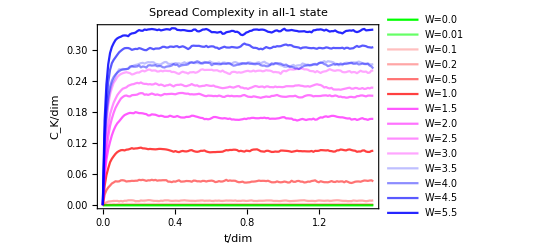

```mathematica
Show[ListLinePlot[{Transpose[{tList14,KCW0}],Transpose[{tList14,KCW0pt01}],Transpose[{tList14,KCW0pt1}],Transpose[{tList14,KCW0pt2}],Transpose[{tList14,KCW0pt5}],Transpose[{tList14,KCW1}],Transpose[{tList14,KCW1pt5}],Transpose[{tList14,KCW2}],Transpose[{tList14,KCW2pt5}],Transpose[{tList14,KCW3}],Transpose[{tList14,KCW3pt5}],Transpose[{tList14,KCW4}],Transpose[{tList14,KCW4pt5}],Transpose[{tList14,KCW5pt5}]},PlotLegends->{"W=0.0","W=0.01","W=0.1","W=0.2","W=0.5","W=1.0","W=1.5","W=2.0","W=2.5","W=3.0","W=3.5","W=4.0","W=4.5","W=5.5"},PlotStyle->{RGBColor[0,1,0,1],RGBColor[0,1,0,0.6],RGBColor[1,0,0,0.25],RGBColor[1,0,0,0.35],RGBColor[1,0,0,0.55],RGBColor[1,0,0,0.75],RGBColor[1,0,1,0.65],RGBColor[1,0,1,0.55],RGBColor[1,0,1,0.45],RGBColor[1,0,1,0.35],RGBColor[0,0,1,0.25],RGBColor[0,0,1,0.45],RGBColor[0,0,1,0.65],RGBColor[0,0,1,0.85]}],Frame->True,FrameLabel->{Style["t/dim",Bold,Black,16],Style["C_K/dim",Bold,Black,16]},PlotLabel->Style["Spread Complexity in all-1 state",Bold,Black]]
```

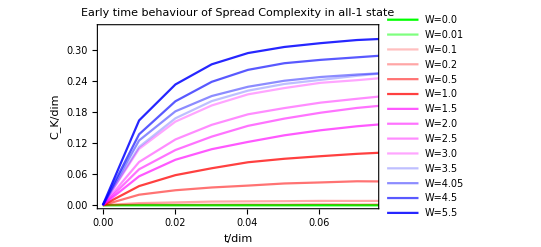

```mathematica
Show[ListLinePlot[{Transpose[{tList14,KCW0}],Transpose[{tList14,KCW0pt01}],Transpose[{tList14,KCW0pt1}],Transpose[{tList14,KCW0pt2}],Transpose[{tList14,KCW0pt5}],Transpose[{tList14,KCW1}],Transpose[{tList14,KCW1pt5}],Transpose[{tList14,KCW2}],Transpose[{tList14,KCW2pt5}],Transpose[{tList14,KCW3}],Transpose[{tList14,KCW3pt5}],Transpose[{tList14,KCW4}],Transpose[{tList14,KCW4pt5}],Transpose[{tList14,KCW5pt5}]},PlotLegends->{"W=0.0","W=0.01","W=0.1","W=0.2","W=0.5","W=1.0","W=1.5","W=2.0","W=2.5","W=3.0","W=3.5","W=4.05","W=4.5","W=5.5"},PlotStyle->{RGBColor[0,1,0,1],RGBColor[0,1,0,0.5],RGBColor[1,0,0,0.25],RGBColor[1,0,0,0.35],RGBColor[1,0,0,0.55],RGBColor[1,0,0,0.75],RGBColor[1,0,1,0.65],RGBColor[1,0,1,0.55],RGBColor[1,0,1,0.45],RGBColor[1,0,1,0.35],RGBColor[0,0,1,0.25],RGBColor[0,0,1,0.45],RGBColor[0,0,1,0.65],RGBColor[0,0,1,0.85]}],Frame->True,FrameLabel->{Style["t/dim",Bold,Black,16],Style["C_K/dim",Bold,Black,16]},PlotRange->{{0,0.075},Automatic},PlotLabel->Style["Early time behaviour of Spread Complexity in all-1 state",Bold,Black]]
```

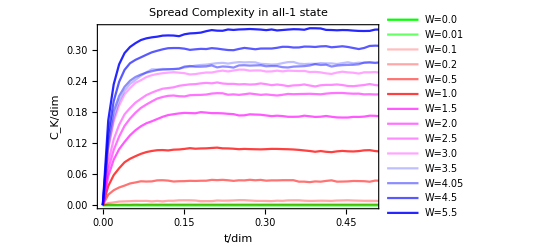

```mathematica
Show[ListLinePlot[{Transpose[{tList14,KCW0}],Transpose[{tList14,KCW0pt01}],Transpose[{tList14,KCW0pt1}],Transpose[{tList14,KCW0pt2}],Transpose[{tList14,KCW0pt5}],Transpose[{tList14,KCW1}],Transpose[{tList14,KCW1pt5}],Transpose[{tList14,KCW2}],Transpose[{tList14,KCW2pt5}],Transpose[{tList14,KCW3}],Transpose[{tList14,KCW3pt5}],Transpose[{tList14,KCW4}],Transpose[{tList14,KCW4pt5}],Transpose[{tList14,KCW5pt5}]},PlotLegends->{"W=0.0","W=0.01","W=0.1","W=0.2","W=0.5","W=1.0","W=1.5","W=2.0","W=2.5","W=3.0","W=3.5","W=4.05","W=4.5","W=5.5"},PlotStyle->{RGBColor[0,1,0,1],RGBColor[0,1,0,0.6],RGBColor[1,0,0,0.25],RGBColor[1,0,0,0.35],RGBColor[1,0,0,0.55],RGBColor[1,0,0,0.75],RGBColor[1,0,1,0.65],RGBColor[1,0,1,0.55],RGBColor[1,0,1,0.45],RGBColor[1,0,1,0.35],RGBColor[0,0,1,0.25],RGBColor[0,0,1,0.45],RGBColor[0,0,1,0.65],RGBColor[0,0,1,0.85]}],Frame->True,FrameLabel->{Style["t/dim",Italic,Black,16],Style["C_K/dim",Italic,Black,16]},PlotRange->{{0,0.5},Automatic},PlotLabel->Style["Spread Complexity in all-1 state",Bold,Black]]
```

## Full Plots KIPR

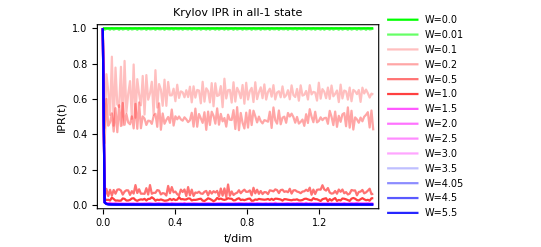

```mathematica
Show[ListLinePlot[{Transpose[{tList14,KIPRW0}],Transpose[{tList14,KIPRW0pt01}],Transpose[{tList14,KIPRW0pt1}],Transpose[{tList14,KIPRW0pt2}],Transpose[{tList14,KIPRW0pt5}],Transpose[{tList14,KIPRW1}],Transpose[{tList14,KIPRW1pt5}],Transpose[{tList14,KIPRW2}],Transpose[{tList14,KIPRW2pt5}],Transpose[{tList14,KIPRW3}],Transpose[{tList14,KIPRW3pt5}],Transpose[{tList14,KIPRW4}],Transpose[{tList14,KIPRW4pt5}],Transpose[{tList14,KIPRW5pt5}]},PlotLegends->{"W=0.0","W=0.01","W=0.1","W=0.2","W=0.5","W=1.0","W=1.5","W=2.0","W=2.5","W=3.0","W=3.5","W=4.05","W=4.5","W=5.5"},PlotStyle->{RGBColor[0,1,0,1],RGBColor[0,1,0,0.6],RGBColor[1,0,0,0.25],RGBColor[1,0,0,0.35],RGBColor[1,0,0,0.55],RGBColor[1,0,0,0.75],RGBColor[1,0,1,0.65],RGBColor[1,0,1,0.55],RGBColor[1,0,1,0.45],RGBColor[1,0,1,0.35],RGBColor[0,0,1,0.25],RGBColor[0,0,1,0.45],RGBColor[0,0,1,0.65],RGBColor[0,0,1,0.85]}],Frame->True,FrameLabel->{Style["t/dim",Bold,Black,16],Style["IPR(t)",Bold,Black,16]},PlotLabel->Style["Krylov IPR in all-1 state",Bold,Black]]
```

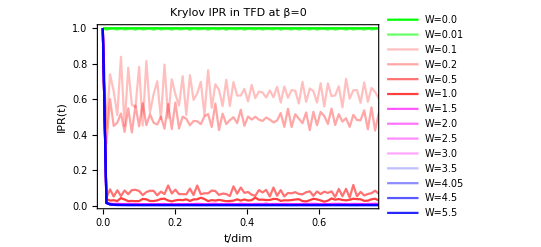

```mathematica
Show[ListLinePlot[{Transpose[{tList14,KIPRW0}],Transpose[{tList14,KIPRW0pt01}],Transpose[{tList14,KIPRW0pt1}],Transpose[{tList14,KIPRW0pt2}],Transpose[{tList14,KIPRW0pt5}],Transpose[{tList14,KIPRW1}],Transpose[{tList14,KIPRW1pt5}],Transpose[{tList14,KIPRW2}],Transpose[{tList14,KIPRW2pt5}],Transpose[{tList14,KIPRW3}],Transpose[{tList14,KIPRW3pt5}],Transpose[{tList14,KIPRW4}],Transpose[{tList14,KIPRW4pt5}],Transpose[{tList14,KIPRW5pt5}]},PlotLegends->{"W=0.0","W=0.01","W=0.1","W=0.2","W=0.5","W=1.0","W=1.5","W=2.0","W=2.5","W=3.0","W=3.5","W=4.05","W=4.5","W=5.5"},PlotStyle->{RGBColor[0,1,0,1],RGBColor[0,1,0,0.6],RGBColor[1,0,0,0.25],RGBColor[1,0,0,0.35],RGBColor[1,0,0,0.55],RGBColor[1,0,0,0.75],RGBColor[1,0,1,0.65],RGBColor[1,0,1,0.55],RGBColor[1,0,1,0.45],RGBColor[1,0,1,0.35],RGBColor[0,0,1,0.25],RGBColor[0,0,1,0.45],RGBColor[0,0,1,0.65],RGBColor[0,0,1,0.85]}],Frame->True,FrameLabel->{Style["t/dim",Bold,Black,16],Style["IPR(t)",Bold,Black,16]},PlotLabel->Style["Krylov IPR in TFD at β=0",Bold,Black],PlotRange->{{0.0,0.75},Full}]
```

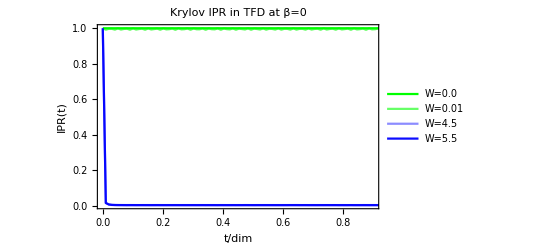

```mathematica
Show[ListLinePlot[{Transpose[{tList14,KIPRW0}],Transpose[{tList14,KIPRW0pt01}],Transpose[{tList14,KIPRW4pt5}],Transpose[{tList14,KIPRW5pt5}]},PlotLegends->{"W=0.0","W=0.01","W=4.5","W=5.5"},PlotStyle->{RGBColor[0,1,0,1],RGBColor[0,1,0,0.6],RGBColor[0,0,1,0.45],RGBColor[0,0,1,0.95]}],Frame->True,FrameLabel->{Style["t/dim",Bold,Black,16],Style["IPR(t)",Bold,Black,16]},PlotLabel->Style["Krylov IPR in TFD at β=0",Bold,Black],PlotRange->{{0,0.9},Full}]
```

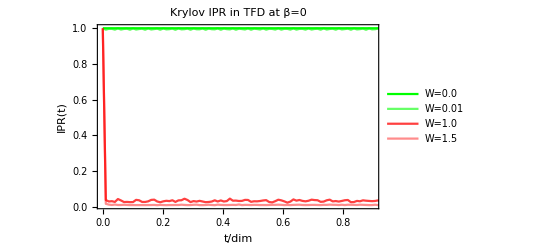

```mathematica
Show[ListLinePlot[{Transpose[{tList14,KIPRW0}],Transpose[{tList14,KIPRW0pt01}],Transpose[{tList14,KIPRW1}],Transpose[{tList14,KIPRW1pt5}]},PlotLegends->{"W=0.0","W=0.01","W=1.0","W=1.5"},PlotStyle->{RGBColor[0,1,0,1],RGBColor[0,1,0,0.6],RGBColor[1,0,0,0.75],RGBColor[1,0,0,0.45]}],Frame->True,FrameLabel->{Style["t/dim",Bold,Black,16],Style["IPR(t)",Bold,Black,16]},PlotLabel->Style["Krylov IPR in TFD at β=0",Bold,Black],PlotRange->{{0,0.9},Full}]
```

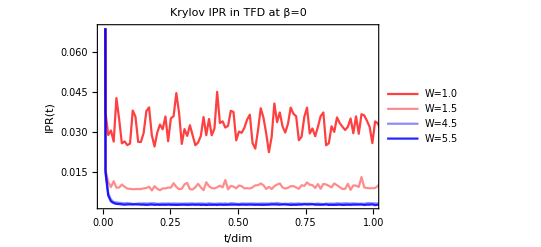

```mathematica
Show[ListLinePlot[{Transpose[{tList14,KIPRW1}],Transpose[{tList14,KIPRW1pt5}],Transpose[{tList14,KIPRW4pt5}],Transpose[{tList14,KIPRW5pt5}]},PlotLegends->{"W=1.0","W=1.5","W=4.5","W=5.5"},PlotStyle->{RGBColor[1,0,0,0.75],RGBColor[1,0,0,0.45],RGBColor[0,0,1,0.45],RGBColor[0,0,1,0.85]}],Frame->True,FrameLabel->{Style["t/dim",Bold,Black,16],Style["IPR(t)",Bold,Black,16]},PlotLabel->Style["Krylov IPR in TFD at β=0",Bold,Black],PlotRange->{{0,1.0},Full}]
```

## Full Plots Entropic Complexity

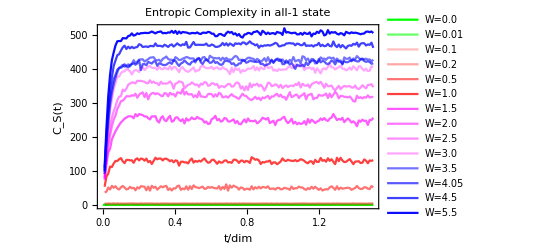

```mathematica
Show[ListLinePlot[{Transpose[{tList14,EntComplexityW0}],Transpose[{tList14,EntComplexityW0pt01}],Transpose[{tList14,EntComplexityW0pt1}],Transpose[{tList14,EntComplexityW0pt2}],Transpose[{tList14,EntComplexityW0pt5}],Transpose[{tList14,EntComplexityW1}],Transpose[{tList14,EntComplexityW1pt5}],Transpose[{tList14,EntComplexityW2}],Transpose[{tList14,EntComplexityW2pt5}],Transpose[{tList14,EntComplexityW3}],Transpose[{tList14,EntComplexityW3pt5}],Transpose[{tList14,EntComplexityW4}],Transpose[{tList14,EntComplexityW4pt5}],Transpose[{tList14,EntComplexityW5pt5}]},PlotLegends->{"W=0.0","W=0.01","W=0.1","W=0.2","W=0.5","W=1.0","W=1.5","W=2.0","W=2.5","W=3.0","W=3.5","W=4.05","W=4.5","W=5.5"},PlotStyle->{RGBColor[0,1,0,1],RGBColor[0,1,0,0.6],RGBColor[1,0,0,0.25],RGBColor[1,0,0,0.35],RGBColor[1,0,0,0.55],RGBColor[1,0,0,0.75],RGBColor[1,0,1,0.65],RGBColor[1,0,1,0.55],RGBColor[1,0,1,0.45],RGBColor[1,0,1,0.35],RGBColor[0,0,1,0.55],RGBColor[0,0,1,0.65],RGBColor[0,0,1,0.75],RGBColor[0,0,1,0.95]}],Frame->True,FrameLabel->{Style["t/dim",Bold,Black,16],Style["C_S(t)",Bold,Black,16]},PlotLabel->Style["Entropic Complexity in all-1 state",Bold,Black]]
```

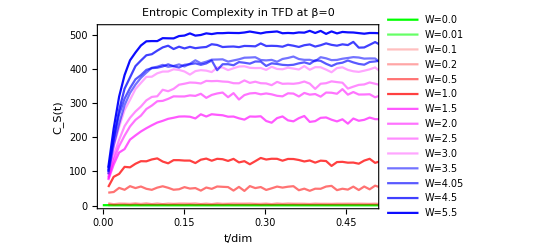

```mathematica
Show[ListLinePlot[{Transpose[{tList14,EntComplexityW0}],Transpose[{tList14,EntComplexityW0pt01}],Transpose[{tList14,EntComplexityW0pt1}],Transpose[{tList14,EntComplexityW0pt2}],Transpose[{tList14,EntComplexityW0pt5}],Transpose[{tList14,EntComplexityW1}],Transpose[{tList14,EntComplexityW1pt5}],Transpose[{tList14,EntComplexityW2}],Transpose[{tList14,EntComplexityW2pt5}],Transpose[{tList14,EntComplexityW3}],Transpose[{tList14,EntComplexityW3pt5}],Transpose[{tList14,EntComplexityW4}],Transpose[{tList14,EntComplexityW4pt5}],Transpose[{tList14,EntComplexityW5pt5}]},PlotLegends->{"W=0.0","W=0.01","W=0.1","W=0.2","W=0.5","W=1.0","W=1.5","W=2.0","W=2.5","W=3.0","W=3.5","W=4.05","W=4.5","W=5.5"},PlotStyle->{RGBColor[0,1,0,1],RGBColor[0,1,0,0.6],RGBColor[1,0,0,0.25],RGBColor[1,0,0,0.35],RGBColor[1,0,0,0.55],RGBColor[1,0,0,0.75],RGBColor[1,0,1,0.65],RGBColor[1,0,1,0.55],RGBColor[1,0,1,0.45],RGBColor[1,0,1,0.35],RGBColor[0,0,1,0.55],RGBColor[0,0,1,0.65],RGBColor[0,0,1,0.75],RGBColor[0,0,1,0.95]}],Frame->True,FrameLabel->{Style["t/dim",Bold,Black,16],Style["C_S(t)",Bold,Black,16]},PlotLabel->Style["Entropic Complexity in TFD at β=0",Bold,Black],PlotRange->{{0.0,0.5},Full}]
```

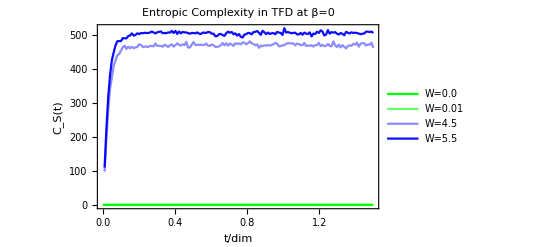

```mathematica
Show[ListLinePlot[{Transpose[{tList14,EntComplexityW0}],Transpose[{tList14,EntComplexityW0pt01}],Transpose[{tList14,EntComplexityW4pt5}],Transpose[{tList14,EntComplexityW5pt5}]},PlotLegends->{"W=0.0","W=0.01","W=4.5","W=5.5"},PlotStyle->{RGBColor[0,1,0,1],RGBColor[0,1,0,0.6],RGBColor[0,0,1,0.45],RGBColor[0,0,1,0.95]}],Frame->True,FrameLabel->{Style["t/dim",Bold,Black,16],Style["C_S(t)",Bold,Black,16]},PlotLabel->Style["Entropic Complexity in TFD at β=0",Bold,Black]]
```

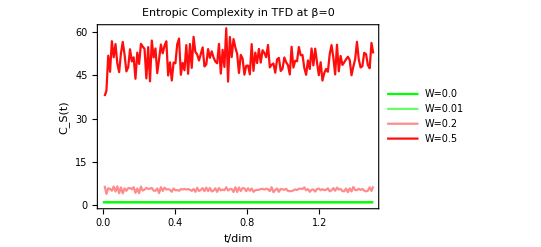

```mathematica
Show[ListLinePlot[{Transpose[{tList14,EntComplexityW0}],Transpose[{tList14,EntComplexityW0pt01}],Transpose[{tList14,EntComplexityW0pt2}],Transpose[{tList14,EntComplexityW0pt5}]},PlotLegends->{"W=0.0","W=0.01","W=0.2","W=0.5"},PlotStyle->{RGBColor[0,1,0,1],RGBColor[0,1,0,0.6],RGBColor[1,0,0,0.45],RGBColor[1,0,0,0.95]}],Frame->True,FrameLabel->{Style["t/dim",Bold,Black,16],Style["C_S(t)",Bold,Black,16]},PlotLabel->Style["Entropic Complexity in TFD at β=0",Bold,Black]]
```

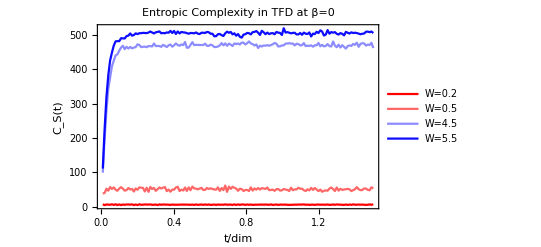

```mathematica
Show[ListLinePlot[{Transpose[{tList14,EntComplexityW0pt2}],Transpose[{tList14,EntComplexityW0pt5}],Transpose[{tList14,EntComplexityW4pt5}],Transpose[{tList14,EntComplexityW5pt5}]},PlotLegends->{"W=0.2","W=0.5","W=4.5","W=5.5"},PlotStyle->{RGBColor[1,0,0,1],RGBColor[1,0,0,0.6],RGBColor[0,0,1,0.45],RGBColor[0,0,1,0.95]}],Frame->True,FrameLabel->{Style["t/dim",Bold,Black,16],Style["C_S(t)",Bold,Black,16]},PlotLabel->Style["Entropic Complexity in TFD at β=0",Bold,Black],PlotRange->{Full,Full}]
```

## Peak vs. W

```mathematica
peakList = {Max[KCW0pt1]-KCW0pt1[[-1]],Max[KCW0pt2]-KCW0pt2[[-1]],Max[KCW0pt5]-KCW0pt5[[-1]],Max[KCW1]-KCW1[[-1]],Max[KCW1pt5]-KCW1pt5[[-1]],Max[KCW2]-KCW2[[-1]],Max[KCW2pt5]-KCW2pt5[[-1]],Max[KCW3]-KCW3[[-1]],Max[KCW3pt5]-KCW3pt5[[-1]],Max[KCW4]-KCW4[[-1]],Max[KCW4pt5]-KCW4pt5[[-1]],Max[KCW5pt5]-KCW5pt5[[-1]]};
wList = {0.1,0.2,0.5,1,1.5,2,2.5,3,3.5,4,4.5,5.5};
```

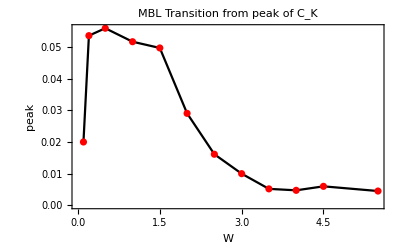

```mathematica
peakWL12=Show[ListLinePlot[Transpose[{wList,peakList}],PlotStyle->Black],ListPlot[Transpose[{wList,peakList}],PlotStyle->Red],Frame->True,FrameLabel->{Style["W",Italic,Black,14],Style["peak",Italic,Black,14]},PlotLabel->Style["MBL Transition from peak of C_K",Bold,Black,16]]
```

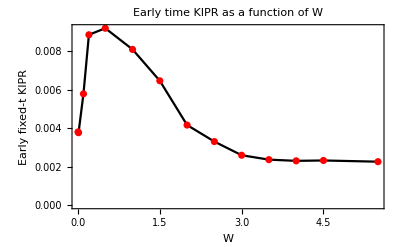

```mathematica
KIPRWFixedtL12 = {KIPRW0[[12]],KIPRW0pt01[[12]],KIPRW0pt1[[12]],KIPRW0pt2[[12]],KIPRW0pt5[[12]],KIPRW1[[12]],KIPRW1pt5[[12]],KIPRW2[[12]],KIPRW2pt5[[12]],KIPRW3[[12]],KIPRW3pt5[[12]],KIPRW4[[12]],KIPRW4pt5[[12]],KIPRW5pt5[[12]]};
wList2= {0,0.01,0.1,0.2,0.5,1,1.5,2.0,2.5,3,3.5,4,4.5,5.5};
Show[ListLinePlot[Transpose[{wList2,KIPRWFixedtL12}],PlotStyle->Black],ListPlot[Transpose[{wList2,KIPRWFixedtL12}],PlotStyle->Red],Frame->True,FrameLabel->{Style["W",Italic,Black,14],Style["Early fixed-t KIPR",Italic,Black,14]},PlotLabel->Style["Early time KIPR as a function of W",Bold,Black,16]]
```

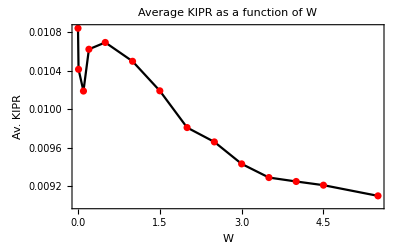

```mathematica
KIPRWavL12 = {KIPRW0//Mean,KIPRW0pt01//Mean,KIPRW0pt1//Mean,KIPRW0pt2//Mean,KIPRW0pt5//Mean,KIPRW1//Mean,KIPRW1pt5//Mean,KIPRW2//Mean,KIPRW2pt5//Mean,KIPRW3//Mean,KIPRW3pt5//Mean,KIPRW4//Mean,KIPRW4pt5//Mean,KIPRW5pt5//Mean};
wList2= {0,0.01,0.1,0.2,0.5,1,1.5,2.0,2.5,3,3.5,4,4.5,5.5};
Show[ListLinePlot[Transpose[{wList2,KIPRWavL12}],PlotStyle->Black],ListPlot[Transpose[{wList2,KIPRWavL12}],PlotStyle->Red],Frame->True,FrameLabel->{Style["W",Italic,Black,14],Style["Av. KIPR",Italic,Black,14]},PlotLabel->Style["Average KIPR as a function of W",Bold,Black,16]]
```